# New in Wolfram Language 12.1 Video, Audio and Image

## Shadi Ashnai, Algorithm R&D, Wolfram Research, Inc.

## Outline

Video [New in 12.1] [Experimental]

The Video Object

Part Extraction

Analysis & Processing

Video Streams & Programmatic Playback

Using FFmpegTools Functions

Video Generation from Manipulates

Extensive Import/Export Support

Audio Updates

Speech Analysis

Speaker Analysis

Other Incremental Updates

Image Updates

Face Detection, Alignment & Analysis

Text Detection & Recognition

Other Incremental Updates

## Video—The Video Object

Version 12.1 of the Wolfram Language™ introduces the Video object as a new first-class citizen.

### What Is Special

The Video object is completely out-of-core.

Supports an extensive list of containers and codecs.

Bundled with complete stacks for image and audio processing.

Bundled with powerful machine learning and neural nets.

Bundled with statistics, visualization and many more capabilities.

### Let’s Begin

Create a Video object from a video file:

```mathematica
v=Video["ExampleData/bullfinch.mkv"]
```

```mathematica
VideoQ[v]
```

```mathematica
Information[v]
```

Create a Video object from a URL:

```mathematica
v=Video["http://exampledata.wolfram.com/agent327.mp4"]
```

```mathematica
Duration[v]
```

Use the Appearance option to select the video GUI:

```mathematica
Video["ExampleData/bullfinch.mkv",Appearance->"Thumbnail"]
```

```mathematica
Video["ExampleData/bullfinch.mkv",Appearance->"Minimal"]
```

```mathematica
Video["ExampleData/bullfinch.mkv",Appearance->"Basic"]
```

Notice that files with multiple video, audio and subtitle tracks are supported:

```mathematica
SetOptions[Video,Appearance->"Minimal"]
```

## Video—Part Extraction

### Frame Extraction

VideoExtractFrames can be used to extract frames from a video using a time quantity or a quantity of a "Frames" unit. Numbers with no units are typically assumed to be in seconds.

Extract one or multiple frames:

```mathematica
v=Video["ExampleData/Caminandes.mp4"]
```

```mathematica
VideoExtractFrames[v,10]
```

```mathematica
VideoExtractFrames[v,{10,20,30}]
```

Specify a time or frames quantity:

```mathematica
VideoExtractFrames[v,QuantityArray[{10,20,30},"Seconds"]]
```

```mathematica
VideoExtractFrames[v,QuantityArray[{100,200,300},"Frames"]]
```

Uniformly sample frames using VideoFrameList:

```mathematica
VideoFrameList[v,3]
```

Create a thumbnail grid from sample frames:

```mathematica
VideoFrameList[v,9]//ImageCollage
```

### Trimming

VideoTrim is the first editing operation introduced in Version 12.1. More editing functions are coming soon.

Trim the first 10 seconds:

```mathematica
VideoTrim[v,10]
```

Trim a sequence of frames:

```mathematica
VideoTrim[v,{Quantity[100,"Frames"],Quantity[200,"Frames"]}]
```

### Audio Selection and Processing

The audio track of a Video object can be extracted and processed using the Audio object:

```mathematica
a=Audio[v]
```

```mathematica
Spectrogram[a]
```

```mathematica
AudioLocalMeasurements[a,"MinMax",PartitionGranularity->1]//ListLinePlot
```

```mathematica
AudioTimeStretch[a,.5]
```

### Track Selection

As mentioned before, video files with multiple video, audio and subtitle tracks are supported. Selecting the video track of interest can be done using the VideoTracks option.

By default, VideoExtractFrames extracts from the first track:

```mathematica
file=FileNameJoin[{NotebookDirectory[],"multiple-tracks-vp9.mkv"}];
```

```mathematica
Import[file,"Summary"]
```

```mathematica
VideoExtractFrames[Video[file],3]
```

Extract from the second track:

```mathematica
VideoExtractFrames[Video[file],3,VideoTracks->2]
```

By default, VideoTrim trims all tracks:

```mathematica
v=Video["ExampleData/bullfinch.mkv"];
Information[v]
```

```mathematica
VideoTrim[v,5]//Information
```

Specify tracks of interest:

```mathematica
VideoTrim[v,5,AudioTracks->1,SubtitleTracks->None]//Information
```

## Video—Video Analysis

The function VideoTimeSeries can be used to detect temporal or spatial events in videos, such as object detection, motion detection or activity recognition.

### Mean Intensity per Frame

```mathematica
v=Video["ExampleData/Caminandes.mp4"];
```

```mathematica
ts=VideoTimeSeries[ImageMeasurements[#,"MeanIntensity"]&,v]
```

TimeSeries[…]

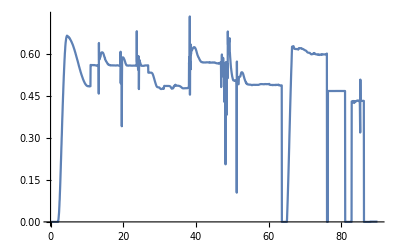

```mathematica
ListLinePlot[ts]
```

### Mean Color per Frame

```mathematica
ts=VideoTimeSeries[ImageMeasurements[#,"Mean"]&,v]
```

TimeSeries[…]

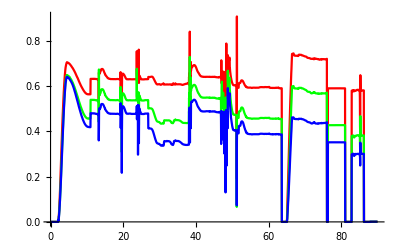

```mathematica
ListLinePlot[ts,PlotStyle->{Red,Green,Blue}]
```

### Number of Cars per Frame

```mathematica
v=Import["http://exampledata.wolfram.com/cars.avi"]
```

-Graphics-

```mathematica
ts=VideoTimeSeries[Length@ImageCases[#,Entity["Concept","Auto::p735c"]]&,v]
```

TimeSeries[…]

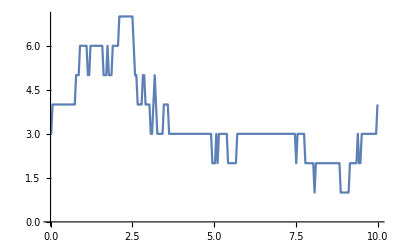

```mathematica
ts//ListLinePlot
```

### Position of Moving Cars

```mathematica
ts=VideoTimeSeries[Point@ImagePosition[#,Entity["Concept","Auto::p735c"]]&,v]
```

TimeSeries[…]

```mathematica
HighlightImage[VideoExtractFrames[v,1],Flatten[Values[ts]]]
```

-Graphics-

### Difference of Consecutive Frames (Simple Scene Detection)

```mathematica
v=Video[FileNameJoin[{NotebookDirectory[],"Musician.mp4"}]]
```

Video[/Users/shadi/Desktop/NewIn121/Musician.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Desktop/NewIn121/Musician.mp4Thumbnail1StandardForm

```mathematica
fr=Information[v,"VideoTracks"][1,"FrameRate"];
diffs=VideoTimeSeries[ImageDistance@@#&,v,Quantity[2, "Frames"],Quantity[1, "Frames"]]
```

TimeSeries[…]

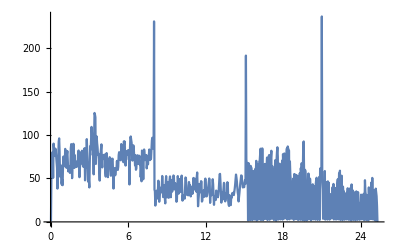

```mathematica
ListLinePlot[diffs,PlotRange->All]
```

```mathematica
FindPeaks[diffs,Automatic,Automatic,150]["Times"]
```

{8.008,15.1151,20.9876}

## Video—Video Processing

The function VideoFrameMap can be used to filter video frames and save them into a new video. It can be used to improve video quality or modify video content, including noise reduction, brightness adjustments, video stabilization, stylization and more.

### Negate Image Frame

```mathematica
v=Video["ExampleData/bullfinch.mkv"];
```

```mathematica
VideoFrameMap[ColorNegate,v]
```

### Highlight Faces

```mathematica
v=Video[FileNameJoin[{NotebookDirectory[],"Faces.mov"}]]
```

```mathematica
VideoFrameMap[Rasterize@HighlightImage[#,FindFaces]&,v];
```

```mathematica
Video[FileNameJoin[{NotebookDirectory[],"FacesHighlighted.mp4"}]]
```

### Highlight Detected Objects

```mathematica
v=Video[FileNameJoin[{NotebookDirectory[],"Restaurant - 910.mp4"}]];
```

```mathematica
VideoFrameMap[Rasterize@HighlightImage[#,ImageBoundingBoxes]&,v,FileNameJoin[{NotebookDirectory[],"RestaurantHighlighted.mp4"}]];
```

```mathematica
Video[FileNameJoin[{NotebookDirectory[],"RestaurantHighlighted.mp4"}]]
```

### Semantic Segmentation

```mathematica
v=Video[FileNameJoin[{NotebookDirectory[],"Street - 22516.mp4"}]]
```

```mathematica
segment[img_,device_:"CPU"]:=Block[{net,encData,dec,mean,var,prob},net=NetModel["Dilated ResNet-38 Trained on Cityscapes Data"];
encData=Normal@NetExtract[net,"input_0"];
dec=NetExtract[net,"Output"];
{mean,var}=Lookup[encData,{"MeanImage","VarianceImage"}];
Colorize@NetReplacePart[net,{"input_0"->NetEncoder[{"Image",ImageDimensions@img,"MeanImage"->mean,"VarianceImage"->var}],"Output"->dec}][img,TargetDevice->device]]
```

```mathematica
VideoFrameMap[segment,v,FileNameJoin[{NotebookDirectory[],"StreetColorized.mp4"}]];
```

```mathematica
Video[FileNameJoin[{NotebookDirectory[],"StreetColorized.mp4"}]]
```

### Motion Stabilization

Look at a video stabilization example from the Wolfram Language 12.0 product pages [link]. This example can be done completely out-of-core using the 12.1 features:

```mathematica
v=Video[FileNameJoin[{NotebookDirectory[],"soap_bubble.mp4"}]]
```

```mathematica
mask = -Graphics-;
```

```mathematica
f=Identity;
VideoFrameMap[Module[{tmp},tmp=Last@FindGeometricTransform[##,TransformationClass->"Rigid"]&@@ImageCorrespondingPoints[Sequence@@#,MaxFeatures->25,Method->"ORB", Masking-> mask];
f=Composition[tmp,f];
ImagePerspectiveTransformation[#[[2]],f,DataRange->Full,Padding->"Fixed"]]&,v,Quantity[2,"Frames"],Quantity[1,"Frames"]];
```

```mathematica
Video[FileNameJoin[{NotebookDirectory[],"soap_stabilized.mp4"}]]
```

## Video—Streams and Programmatic Playback

VideoStream is a handle to a Video object for programmatic playback and processing.

### VideoStream

```mathematica
str=VideoStream["ExampleData/bullfinch.mkv"]
```

```mathematica
Dynamic[str["Position"]]
```

```mathematica
Dynamic[str["CurrentFrame"]]
```

```mathematica
VideoPlay[str]
```

Check all stream properties:

```mathematica
AssociationMap[str,str["Properties"]]//Dataset
```

Pause or stop the stream:

```mathematica
VideoPause[str]
```

```mathematica
VideoStop[str]
```

### Create a Simple Video Player

```mathematica
Panel@Column[{
Dynamic[str["CurrentFrame"]],
Slider[Dynamic[QuantityMagnitude[str["Position"],"Seconds"],(str["Position"]=#)&],{0,QuantityMagnitude[str["Duration"],"Seconds"]}],
 Button[
Dynamic[If[str["Status"]==="Playing","Pause","Play"]],
If[str["Status"]==="Playing",VideoPause[str],VideoPlay[str]]
]
}, Alignment->Center]
```

```mathematica
VideoStop[str]
```

### Process the Video Stream

Apply a neural network–based function to the current frame in real time:

```mathematica
VideoPlay[str];HighlightImage[str["CurrentFrame"],ImageCases[str["CurrentFrame"],All->"BoundingBox"]]//Dynamic
```

```mathematica
VideoStop[]
```

## Video—Using FFmpegTools Filters

FFmpeg is one of the backends for importing, processing, analyzing and exporting video files. Some experiments have been done with directly using FFmpeg filters to process a video.

### ColorNegate

```mathematica
v=Video[FileNameJoin[{NotebookDirectory[],"soap_bubble.mp4"}]];
```

```mathematica
VideoFrameMap[{{"lutrgb","r","negval","g","negval","b","negval"}}, v]
```

Video[/Users/shadi/Documents/Wolfram/Video/soap_bubble-6639b889-160b-40b8-a810-1653822c94ea.mkv,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/soap_bubble-6639b889-160b-40b8-a810-1653822c94ea.mkvThumbnail1StandardForm

```mathematica
AbsoluteTiming[VideoFrameMap[{{"lutrgb","r","negval","g","negval","b","negval"}}, v]//VideoQ]
```

{2.87972,True}

```mathematica
AbsoluteTiming[VideoFrameMap[ColorNegate, v]//VideoQ]
```

{7.97603,True}

### Stabilization

```mathematica
VideoFrameMap[{{"deshake"}}, v]
```

Video[/Users/shadi/Documents/Wolfram/Video/soap_bubble-61679d59-1f7a-4d02-b52b-4403a4faf93b.mkv,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/soap_bubble-61679d59-1f7a-4d02-b52b-4403a4faf93b.mkvThumbnail1StandardForm

### ImageReflect

```mathematica
AbsoluteTiming[VideoFrameMap[{{"vflip"}}, v]//VideoQ]
```

{3.27302,True}

```mathematica
AbsoluteTiming[VideoFrameMap[ImageReflect, v]//VideoQ]
```

{6.75003,True}

### EdgeDetect

```mathematica
AbsoluteTiming[VideoFrameMap[{{"edgedetect"}}, v]//VideoQ]
```

{4.85346,True}

```mathematica
AbsoluteTiming[VideoFrameMap[EdgeDetect, v]//VideoQ]
```

{20.388,True}

### ImageResize

```mathematica
AbsoluteTiming[VideoFrameMap[{{"scale", "w","iw/2","h","ih/2"}}, v]//VideoQ]
```

{2.16161,True}

```mathematica
AbsoluteTiming[VideoFrameMap[ImageResize[#,Scaled[0.5]]&, v]//VideoQ]
```

{9.18707,True}

## Video—Generation from Manipulates

Manipulate, ListAnimate and Animate are powerful functions for generating animations in the Wolfram Language. You can create Video objects or export them to video files with or without audio.

### Video from a Manipulate

```mathematica
Video[Manipulate[Plot[Sin[a x],{x,0,2π}],{a,1,10},ControlType->None,Paneled->False]]
```

### Export a Manipulate

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"file.mp4"}],Manipulate[Plot[Sin[a x],{x,0,2π}],{a,1,10}]];
```

```mathematica
Video[FileNameJoin[{NotebookDirectory[],"file.mp4"}]]
```

### Export a Manipulate with Sound

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"file2.mp4"}],{"Animation"->Manipulate[Plot[Sin[a x],{x,0,2π}],{a,1,10}],"Audio"->Audio@Sound[Table[SoundNote[i],{i,4}]]},"Rules"];
```

```mathematica
Video[FileNameJoin[{NotebookDirectory[],"file2.mp4"}]]
```

## Video—Supported Codecs

The Wolfram Language by default uses the operating system as well as a limited version of FFmpeg for decoding and encoding a large number of multimedia containers and codecs.

### Video Import

Supported video formats for Import:

```mathematica
$VideoDecoders//Keys
```

Available video decoders per container:

```mathematica
$VideoDecoders//Dataset
```

Available MP4 video decoders:

```mathematica
$VideoDecoders["MP4"][[All,1]]
```

### Video Export

Supported video formats for Export:

```mathematica
$VideoEncoders//Keys
```

Available video encoders per container:

```mathematica
$VideoEncoders//Dataset
```

Available MP4 encoders:

```mathematica
$VideoEncoders["MP4"][[All,1]]
```

### Audio and Subtitle Codecs

Available audio decoders and encoders in MP4 files:

```mathematica
$AudioDecoders["MP4"][[All,1]]
```

```mathematica
$AudioEncoders["MP4"][[All,1]]
```

Available subtitle decoders and encoders for Matroska:

```mathematica
$SubtitleDecoders["Matroska"][[All,1]]
```

```mathematica
$SubtitleEncoders["Matroska"][[All,1]]
```

### Installing FFmpeg

Install FFmpeg Version 4.0.0 or higher to get a more complete codec support. See the following for platform-specific instructions.

With FFmpeg installed, the Wolfram Language makes use of it by default.

Check system options for video processing:

```mathematica
SystemOptions["VideoProcessingOptions"]
```

{VideoProcessingOptions→{TryUsingSystemFFmpeg→True}}

Supported video decoders:

```mathematica
Length/@$VideoDecoders
```

<|AVI→141,Matroska→237,MP4→21,Ogg→1,QuickTime→63,VideoFormat→259|>

Quit and explicitly disable the use of the installed FFmpeg:

```mathematica
Quit
```

```mathematica
SetSystemOptions["VideoProcessingOptions"->{"TryUsingSystemFFmpeg"->False}]
```

VideoProcessingOptions→{TryUsingSystemFFmpeg→False}

Notice the reduced number of decoders supported for each container:

```mathematica
Length/@$VideoDecoders
```

<|AVI→37,Matroska→54,MP4→13,Ogg→1,QuickTime→28,VideoFormat→71|>

Check here for more details including instructions for installing FFmpeg.

## Audio—Updates

Speech Analysis

Speaker Analysis

Other Incremental Updates

## Audio—Speech Analysis

### Interpret Speech

SpeechInterpreter is a function that tries to interpret the result of SpeechRecognize:

```mathematica
SpeechInterpreter["SemanticNumber"][]
```

```mathematica
SpeechInterpreter["ComputedDate"][]
```

```mathematica
SpeechInterpreter["Country"][]
```

A future plan would be for speech-enabled form functions. Possibly FormFunction and AskFunction supporting speech inputs, where the input is automatically transcribed, interpreted and used.

### Find Speech Cases

SpeechCases pipes the output of SpeechRecognize to TextCases to find spoken cases of a special type:

```mathematica
SpeechCases[,"Noun"]
```

```mathematica
SpeechCases[,"CurrencyAmount"->"Interpretation"]
```

```mathematica
SpeechCases[,{"City","Country"}->{"String","Interpretation","Probability"}]
```

### Compute Speech Properties

AudioLocalMeasurements introduces new speech properties, such as spectral envelope and aperiodicity:

```mathematica
a=SpeechSynthesize["Hello, this is a test recording."]
```

```mathematica
MatrixPlot[Transpose[Reverse/@Values[AudioLocalMeasurements[a,"SpeechSpectralEnvelope"]]],AspectRatio->1]
```

```mathematica
MatrixPlot[Transpose[Reverse/@Values[AudioLocalMeasurements[a,"SpeechAperiodicity"]]],AspectRatio->1]
```

### Find Voiced Intervals

Use AudioIntervals or AudioLocalMeasurements to find the voice activity in an audio recording:

```mathematica
AudioLocalMeasurements[a,"VoiceActivity"]//ListLinePlot
```

```mathematica
AudioIntervals[a,"VoiceActivity"]
```

```mathematica
AudioPlot[a,Epilog->{RGBColor[1,0,0,.5],Rectangle[{#[[1]],-1},{#[[2]],1}]&/@%}]
```

### Time Stretch or Pitch Shift using “Speech”

PitchRecognize, AudioTimeStretch and AudioPitchShift now have a method specific for speech signals:

```mathematica
ListLinePlot[PitchRecognize[a,Method->#]&/@{"Speech",Automatic},PlotLegends->{"Speech","Automatic"}]
```

```mathematica
AudioTimeStretch[a,1.5,Method->"Speech"]
```

```mathematica
AudioPitchShift[a,2,Method->"Speech"]
```

## Audio—Speaker Analysis

### Speaker Classification

A net has been trained to perform speaker classification. The net was trained on the VoxCeleb 2 dataset (over one million recordings from about 6000 speakers):

```mathematica
net=NetModel["SpeakerClassificationAlex"]
```

The structure is inspired by AlexNet (extremely simple), but adapted to accept variable-length inputs:

```mathematica
Information[NetModel["SpeakerClassificationAlex"],"SummaryGraphic"]
```

This is still just an experiment and further trainings will be performed. For now, this simple classification can be used as is:

```mathematica
a=ExampleData[{"Audio","MaleVoice"}];
```

```mathematica
net[a]
```

### Speaker Feature Extractors

While classifying a voice among a list of 6000 “celebrities” is amusing, it does not really serve any practical purpose. What can be interesting instead is the use of the same net as a feature extractor to compute features that are semantically significant to differentiate voices.

Here is a variation of the previous net that returns a 1024-length speaker feature vector for an audio recording that is semantically significant in the space of different voices:

```mathematica
net=NetModel["AlexFineTunedSpeakerClassification"]
```

```mathematica
net[a]//Short
```

```mathematica
ListLinePlot[net[a],PlotRangePadding->.1,AspectRatio->1/3]
```

Two new speaker feature extractors have been introduced based on this net: "SpeakerFeatures" and "SpeakerFeatureVector", which can be used in other functions such as Classify, FeatureSpacePlot, etc.

Use test data from the Spoken Digit Commands dataset:

```mathematica
data=Normal[ResourceData["Spoken Digit Commands","TestDataset"]];
RandomChoice[data]
```

Separate data by the speaker:

```mathematica
grouped=SortBy[GroupBy[data,#SpeakerID&],Minus@*Length];
color=AssociationThread[Keys[grouped]->(ColorData[97]/@Range[Length[grouped]])];
```

```mathematica
Keys[grouped]//Length
```

```mathematica
Keys[grouped]//Short
```

FeatureSpacePlot using the "SpeakerFeatureVector" feature shows a semantically meaningful speaker embedding on the dataset:

```mathematica
FeatureSpacePlot[Flatten@Values@Map[Callout[Style[#Input,color[#SpeakerID]],#SpeakerID]&,grouped[[;;5,;;UpTo[20]]],{2}],LabelingFunction->None,FeatureExtractor->"SpeakerFeatureVector",ImageSize->Large]
```

This will allow both transfer learning (not only for speaker recognition, but also as a starting point for age, gender, emotion… classification) and semantic distance computations on speech signals.

### SpeakerMatchQ

SpeakerMatchQ simply compares the speaker features of two speech signals and decides whether two signals were recorded by the same person:

```mathematica
SpeakerMatchQ[ExampleData[{"Audio","FemaleVoice"}],ExampleData[{"Audio","MaleVoice"}]]
```

```mathematica
SpeakerMatchQ[ExampleData[{"Audio","FemaleVoice"}],AudioCapture[]]
```

```mathematica
SpeakerMatchQ[AudioCapture[],AudioCapture[]]
```

## Audio—Other Incremental Updates

### AudioInstanceQ

AudioInstanceQ tries to identify whether an audio signal is an instance of a given category:

```mathematica
AudioInstanceQ[ExampleData[{"Audio","DogBark"}],"dog"]
```

```mathematica
AudioInstanceQ[ExampleData[{"Audio","DogBark"}],"cat"]
```

```mathematica
AudioInstanceQ[ExampleData[{"Audio","DogBark"}],"cat"|"dog"]
```

For example, find all instrument recordings in ExampleData["Audio"]:

```mathematica
exampleData=AssociationMap[ExampleData,ExampleData["Audio"]];
```

```mathematica
Select[exampleData,AudioInstanceQ[#,"musical instrument"]&]
```

Available sound classes are:

```mathematica
EntityList["Sound"]//Short
```

### AudioReverse

AudioReverse yields a backward audio to achieve audio effects or understand a hidden message:

```mathematica
AudioReverse[]
```

### AudioStream Updates

AudioStream in Version 12.0 was either linked to an audio source for playback or linked to an input source for capture:

```mathematica
s=AudioStream[Audio["ExampleData/rule30.wav"]]
```

```mathematica
AudioPlay[s]
```

```mathematica
s["Position"]//Dynamic
```

```mathematica
s["Looping"]=True;
```

```mathematica
s["CurrentAudio"]//AudioPlot//Dynamic
```

```mathematica
AudioPlay[s]
```

```mathematica
AudioStop[]
```

Version 12.1 introduces audio streams created from lists of audio. Here is an example:

```mathematica
list=SpeechSynthesize/@{"Hi","How are you?","Bye"};
```

```mathematica
s=AudioStream[list]
```

```mathematica
s["CurrentTrack"]//Dynamic
```

```mathematica
AudioPlay[s];
```

There are additional new properties for these streams:

```mathematica
AssociationMap[s[#]&,s["Properties"]]//Dataset
```

```mathematica
s["Ordering"]={3,1,2};
```

```mathematica
AudioPlay[s]
```

Join, Append, AppendTo and Drop now work on AudioStream objects:

```mathematica
Join[s,s]
```

```mathematica
Join[s,Drop[s,1]]//AudioPlay
```

Streams can also be generated by a function whose argument is the current time. Here is an example of one second of generated sine:

```mathematica
AudioGenerator[Sin[440. 2 Pi#]&]
```

And here is an infinite sine wave:

```mathematica
gen=AudioStream[.2Sin[440. 2 Pi#]&]
```

```mathematica
AudioPlay[gen];
```

```mathematica
gen["Duration"]
```

```mathematica
gen["Position"]//Dynamic
```

```mathematica
AudioStop[gen]
```

This also exposes new properties:

```mathematica
AssociationMap[gen[#]&,gen["Properties"]]//Dataset
```

Dynamically change the frequency of the sine wave:

```mathematica
freq=440;
gen=AudioStream[.2 Sin[freq 2 Pi#]&];
Slider[Dynamic[freq],{400,1000}]
```

```mathematica
AudioPlay[gen];
```

```mathematica
AudioStop[gen]
```

## Image—Updates

Face Detection, Alignment & Analysis

Text Detection & Recognition

Other Incremental Updates

## Image—Face Detection, Alignment & Analysis

### FindFaces

Version 12.0 introduced new methods and significant quality improvement in face detection. Version 12.1 adds padding capability when finding faces:

```mathematica
i=-Graphics-;
```

```mathematica
FindFaces[i,"Image"]
```

```mathematica
FindFaces[i,"Image",PaddingSize->10]
```

### New Facial Features

FacialFeatures introduces simple single-point facial features:

```mathematica
landmarks=FacialFeatures[i,{"LeftEyeCenter","RightEyeCenter","NoseCenter","MouthLeft","MouthRight"}];
```

```mathematica
HighlightImage[i,{PointSize[.01],Merge[landmarks,Identity]},ImageLegends->All,ImageLabels->None,ImageSize->500]
```

### FaceAlign

Face alignment is the process of transforming faces to align certain facial landmarks of multiple faces and is typically used for morphing, comparing or recognizing faces:

```mathematica
FaceAlign[i]
```

```mathematica
Manipulate[Grid[{MapThread[Labeled,{Image[{Blend[FaceAlign[i],a],Blend[FindFaces[i,"Image"],a]},ImageSize->All],Text/@{"aligned","unaligned"}}]},Spacings->{2,1}],{a,0,1}]
```

## Image—Other Updates

### Text Detection

TextRecognize had a significant improvement in Version 12.0. FindImageText is a useful function that tries to find regions of an image corresponding to text:

```mathematica
i=-Graphics-;
```

```mathematica
FindImageText[i]
```

```mathematica
HighlightImage[i,%]
```

```mathematica
FindImageText[i,"Word", "Image"]
```

```mathematica
HighlightImage[i,FindImageText[i,"Word"]]
```

It could be used to improve the result of text recognition:

```mathematica
image=-Graphics-;
TextRecognize[image]
```

```mathematica
subimages=FindImageText[image,"Word","AlignedImage"]
```

Perform OCR and join the results:

```mathematica
TextRecognize[subimages,RecognitionPrior->"Word"]//StringRiffle
```

### Labeling and Legending in HighlightImage

As seen above, HighlightImage is now able to add labels and legends. By default, keys of associations are used as labels or legends:

```mathematica
i=-Graphics-;
```

```mathematica
boxes=ImageBoundingBoxes[i]
```

```mathematica
HighlightImage[i,boxes]
```

Turn off the labels and turn on the legends:

```mathematica
HighlightImage[i,boxes,ImageLabels->None,ImageLegends->All]
```

### ImageAssemble

ImageAssemble in Version 12.1 conforms images to have similar properties and can fit images of different sizes by padding, cropping or resizing images. Other convenient options are added too:

```mathematica
ImageAssemble[Table[EdgeDetect[-Graphics-,r,t],{r,{2,4,6}},{t,{.01,.05,.1}}]]
```

```mathematica
ImageAssemble[Table[EdgeDetect[-Graphics-,r,t],{r,{2,4,6}},{t,{.01,.05,.1}}],Background->Orange,Spacings->5,PaddingSize->5]
```

Here is an example of assembling images with different properties, downloaded from the web:

```mathematica
list=WebImageSearch["fish","Thumbnails",MaxItems->12]
```

```mathematica
ImageAssemble[Partition[list,4],"Fill",Spacings->5,Background->White]
```

It can also nicely handle Missing objects:

```mathematica
paintings=EntityValue[Entity["Person","EugeneDelacroix::77vj8"],EntityProperty["Person","NotableArtworks"]];
data=EntityValue[paintings,"Image"];
```

```mathematica
Length[list]
```

```mathematica
Count[list,_Missing]
```

```mathematica
ImageAssemble[Partition[list,10],"Fill",Spacings->3,PaddingSize->3,Background->White]
```

### Rasterize

Rasterize is now aware of screen resolution:

```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Rasterize[Plot[Sin[x],{x,0,2π}],ImageResolution->72]
```

```mathematica
ImageDimensions[%]
```

```mathematica
Rasterize[Plot[Sin[x],{x,0,2π}]]
```

```mathematica
ImageDimensions[%]
```

```mathematica
"Resolution"/.CurrentValue["ConnectedDisplays"]
```

### Speed Improvements

There are constant speed improvements in the system. Here is a comparison of a call to ImageTransformation on different size images in Versions 12.0 and 12.1:

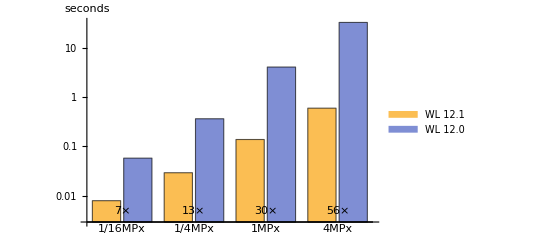

```mathematica
ImageTransformation[image,Sqrt,Resampling->"Linear"]
```

### Import/Export Updates

Version 12.1 significantly improves the speed and quality of DICOM import and introduces support for DICOMDIR:

```mathematica
Import["knee_mr/DICOMDIR","Summary"]
```

```mathematica
Import["knee_mr/DICOMDIR","StructureGraph"]
```

```mathematica
Import["knee_mr/DICOMDIR","CenterImage"]
```

```mathematica
Import["knee_mr/DICOMDIR",{"CenterImage",1,1,3}]
```

Support for the highly efficient HEIF (also known as HEIC) files is also added:

```mathematica
Import["ExampleData/sample.heic"]
```

## References

Video Processing

Importing & Exporting Video

Image Processing

Audio Processing

Speech Computation

## Thanks!